### real frequency to time tutorial complex exponential (easy) +normalization

```mathematica
Clear["Global`*"]
kHz=10^3;
us=10^-6;
k0=50kHz;
Δt=.33us;
n=2^9;

(*how to convert from time to real frequency*)
t=Range[0,n-1]Δt;
rbw=1/(n Δt);
f=Range[0,n-1]rbw;


tproc=Table[Exp[- I 2π k0 t],{t,Range[0,n-1]Δt}];
fproc=Fourier[tproc];

(*fourier normalizes it so that the total power is the same*)
Total[Abs[tproc]^2]
Total[Abs[fproc]^2]
```

512.

512.

```mathematica
(*normalize it by hand so that the integral of PSD are equal. (parsevals' theorem)*)
fprocNorm=fproc √(Δt/rbw);
1. Total[Abs[tproc]^2]Δt
1. Total[Abs[fprocNorm]^2]rbw
```

0.00016896

0.00016896

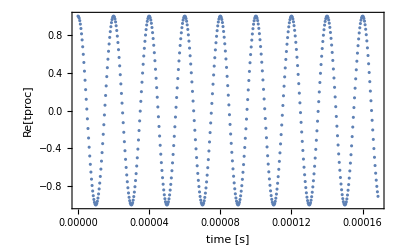

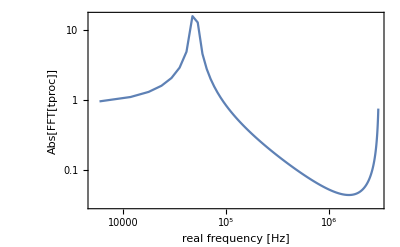

```mathematica
ttproc=Thread[{t,Re[tproc]}];
ffproc=Thread[{f,Abs[fproc]}];
ListPlot[ttproc,Axes->False,Frame->True,FrameLabel->{"time [s]","Re[tproc]","period="<>ToString[1./k0]}]
ListLogLogPlot[ffproc,Axes->False,Frame->True,FrameLabel->{"real frequency [Hz]","Abs[FFT[tproc]]","freq="<>ToString[k0]},PlotRange->All,Joined->True]
```

### from cavity ringdown τ to linewidth: conclusion: 2 1/τ = FWHM [*angular* frequency] 1/(π τ) = FWHM [*real* frequency]

```mathematica
Clear[t,τ,f,ff];
FourierTransform[Exp[-Abs[t]/τ],t,ω]

(*verify that FourierTransform is in angular frequency*)
FourierTransform[Sin[ω0 t],t,ω]
```

(√(2/π) τ)/(1+τ^2 ω^2)

ⅈ √(π/2) DiracDelta[ω-ω0]-ⅈ √(π/2) DiracDelta[ω+ω0]

### numerical study.

```mathematica
Clear["Global`*"]
us=10^-6;
kHz=10^3;
ms=10^-3;
k0= 33kHz;
τ=.02ms;
Δt=1us;
n=2^9;

t=Range[0,n-1]Δt;
rbw=1/(n Δt);
f= Range[0,n-1]rbw;


tproc=Table[Exp[- I 2π k0 t-t/τ],{t,Range[0,n-1]Δt}];
fproc=Fourier[tproc];

(*fourier normalizes it so that the total power is the same*)
Total[Abs[tproc]^2]
Total[Abs[fproc]^2]
```

10.5083

10.5083

```mathematica
(*normalize it by hand so that the integral of PSD are equal. (parsevals' theorem)*)
fprocNorm=fproc √(Δt/rbw);
Total[Abs[tproc]^2]Δt
Total[Abs[fprocNorm]^2]rbw
```

0.0000105083

0.0000105083

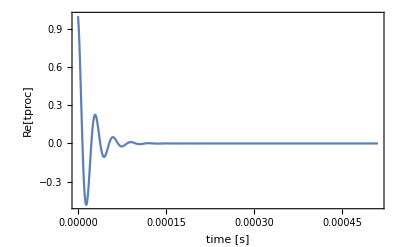

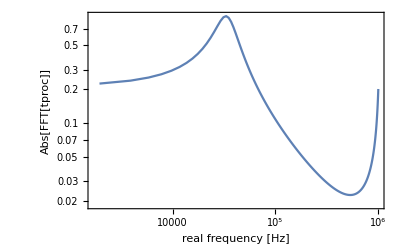

```mathematica
ttproc=Thread[{t,Re[tproc]}];
ffproc=Thread[{f,Abs[fproc]}];

ListPlot[ttproc,Joined->True,Axes->False,Frame->True,FrameLabel->{"time [s]","Re[tproc]","period="<>ToString[1./k0]},PlotRange->All]
ListLogLogPlot[ffproc,Axes->False,Frame->True,FrameLabel->{"real frequency [Hz]","Abs[FFT[tproc]]","freq="<>ToString[k0]},PlotRange->All,Joined->True]
```

```mathematica
maxff=Max[ffproc[[;;,2]]];
FindClusters[1. Cases[ffproc,x_/;Abs[x[[2]]-maxff/2]<maxff/10][[;;,1]]];
Mean[#]&/@%;
FWHM=Differences[%][[1]]; 2π FWHM
```

184078.

```mathematica
(*compare with 2/τ =FHWM in angular freq*)
2/τ
```

100000.

# factor of 2 off WTF>>>>>>